```mathematica
readings={
{5,-42},
{25,-54},
{45,-60},
{60,-70},
{80,-74}
};
```

```mathematica
ExprD2R=Fit[readings,{1,Log10[d]},d]
```

-21.8769-11.1397 Log[d]

```mathematica
ExprR2D=d//.Solve[ExprD2R==r,d][[1]]
```

0.140314 ⅇ^(-0.089769 r)

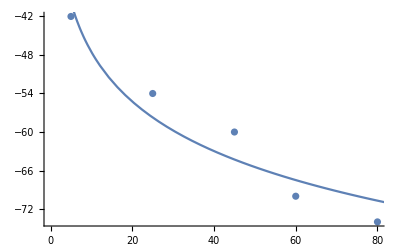

```mathematica
Show[
ListPlot[readings],
Plot[ExprD2R,{d,0,100}]
]
```

```mathematica
ExprR2D//.{r->-78}
```

38.4526

```mathematica
ExprR2D
```

0.209256 ⅇ^(-0.0668413 r)

```mathematica
Coords={a1->0,b1->0,a2->0,b2->1,a3->1,b3->1,a4->1,b4->0};
```

```mathematica
F=Assuming[{
w21∈Reals,
w31∈Reals,
w41∈Reals,
w32∈Reals,
w42∈Reals,
w43∈Reals
},LeastSquares[
{
w21*{a2-a1,b2-b1}//.Coords,
w31*{a3-a1,b3-b1}//.Coords,
w41*{a4-a1,b4-b1}//.Coords,
w32*{a3-a2,b3-b2}//.Coords,
w42*{a4-a2,b4-b2}//.Coords,
w43*{a4-a3,b4-b3}//.Coords
},
{
w21*{((a2^2+b2^2-d2^2)-(a1^2+b1^2-d1^2))/2}//.Coords,
w31*{((a3^2+b3^2-d3^2)-(a1^2+b1^2-d1^2))/2}//.Coords,
w41*{((a4^2+b4^2-d4^2)-(a1^2+b1^2-d1^2))/2}//.Coords,
w32*{((a3^2+b3^2-d3^2)-(a2^2+b2^2-d2^2))/2}//.Coords,
w42*{((a4^2+b4^2-d4^2)-(a2^2+b2^2-d2^2))/2}//.Coords,
w43*{((a4^2+b4^2-d4^2)-(a3^2+b3^2-d3^2))/2}//.Coords
}
]]
```

{{((1+d1^2-d2^2) w21^2 (-w31^2+w42^2))/(2 (w21^2 w31^2+w21^2 w32^2+w31^2 w32^2+w21^2 w41^2+w31^2 w41^2+w21^2 w42^2+4 w31^2 w42^2+w32^2 w42^2+w41^2 w42^2+w31^2 w43^2+w32^2 w43^2+w41^2 w43^2+w42^2 w43^2))-((-1+d3^2-d4^2) (-w31^2+w42^2) w43^2)/(2 (w21^2 w31^2+w21^2 w32^2+w31^2 w32^2+w21^2 w41^2+w31^2 w41^2+w21^2 w42^2+4 w31^2 w42^2+w32^2 w42^2+w41^2 w42^2+w31^2 w43^2+w32^2 w43^2+w41^2 w43^2+w42^2 w43^2))+((1+d2^2-d3^2) w32^2 (w21^2+w31^2+w42^2+w43^2))/(2 (w21^2 w31^2+w21^2 w32^2+w31^2 w32^2+w21^2 w41^2+w31^2 w41^2+w21^2 w42^2+4 w31^2 w42^2+w32^2 w42^2+w41^2 w42^2+w31^2 w43^2+w32^2 w43^2+w41^2 w43^2+w42^2 w43^2))+((1+d1^2-d4^2) w41^2 (w21^2+w31^2+w42^2+w43^2))/(2 (w21^2 w31^2+w21^2 w32^2+w31^2 w32^2+w21^2 w41^2+w31^2 w41^2+w21^2 w42^2+4 w31^2 w42^2+w32^2 w42^2+w41^2 w42^2+w31^2 w43^2+w32^2 w43^2+w41^2 w43^2+w42^2 w43^2))+1/2 (2+d1^2-d3^2) w31 ((w31 (-w31^2+w42^2))/(w21^2 w31^2+w21^2 w32^2+w31^2 w32^2+w21^2 w41^2+w31^2 w41^2+w21^2 w42^2+4 w31^2 w42^2+w32^2 w42^2+w41^2 w42^2+w31^2 w43^2+w32^2 w43^2+w41^2 w43^2+w42^2 w43^2)+(w31 (w21^2+w31^2+w42^2+w43^2))/(w21^2 w31^2+w21^2 w32^2+w31^2 w32^2+w21^2 w41^2+w31^2 w41^2+w21^2 w42^2+4 w31^2 w42^2+w32^2 w42^2+w41^2 w42^2+w31^2 w43^2+w32^2 w43^2+w41^2 w43^2+w42^2 w43^2))+1/2 (d2^2-d4^2) w42 (-((w42 (-w31^2+w42^2))/(w21^2 w31^2+w21^2 w32^2+w31^2 w32^2+w21^2 w41^2+w31^2 w41^2+w21^2 w42^2+4 w31^2 w42^2+w32^2 w42^2+w41^2 w42^2+w31^2 w43^2+w32^2 w43^2+w41^2 w43^2+w42^2 w43^2))+(w42 (w21^2+w31^2+w42^2+w43^2))/(w21^2 w31^2+w21^2 w32^2+w31^2 w32^2+w21^2 w41^2+w31^2 w41^2+w21^2 w42^2+4 w31^2 w42^2+w32^2 w42^2+w41^2 w42^2+w31^2 w43^2+w32^2 w43^2+w41^2 w43^2+w42^2 w43^2))},{((1+d2^2-d3^2) w32^2 (-w31^2+w42^2))/(2 (w21^2 w31^2+w21^2 w32^2+w31^2 w32^2+w21^2 w41^2+w31^2 w41^2+w21^2 w42^2+4 w31^2 w42^2+w32^2 w42^2+w41^2 w42^2+w31^2 w43^2+w32^2 w43^2+w41^2 w43^2+w42^2 w43^2))+((1+d1^2-d4^2) w41^2 (-w31^2+w42^2))/(2 (w21^2 w31^2+w21^2 w32^2+w31^2 w32^2+w21^2 w41^2+w31^2 w41^2+w21^2 w42^2+4 w31^2 w42^2+w32^2 w42^2+w41^2 w42^2+w31^2 w43^2+w32^2 w43^2+w41^2 w43^2+w42^2 w43^2))+((1+d1^2-d2^2) w21^2 (w31^2+w32^2+w41^2+w42^2))/(2 (w21^2 w31^2+w21^2 w32^2+w31^2 w32^2+w21^2 w41^2+w31^2 w41^2+w21^2 w42^2+4 w31^2 w42^2+w32^2 w42^2+w41^2 w42^2+w31^2 w43^2+w32^2 w43^2+w41^2 w43^2+w42^2 w43^2))-((-1+d3^2-d4^2) (w31^2+w32^2+w41^2+w42^2) w43^2)/(2 (w21^2 w31^2+w21^2 w32^2+w31^2 w32^2+w21^2 w41^2+w31^2 w41^2+w21^2 w42^2+4 w31^2 w42^2+w32^2 w42^2+w41^2 w42^2+w31^2 w43^2+w32^2 w43^2+w41^2 w43^2+w42^2 w43^2))+1/2 (2+d1^2-d3^2) w31 ((w31 (-w31^2+w42^2))/(w21^2 w31^2+w21^2 w32^2+w31^2 w32^2+w21^2 w41^2+w31^2 w41^2+w21^2 w42^2+4 w31^2 w42^2+w32^2 w42^2+w41^2 w42^2+w31^2 w43^2+w32^2 w43^2+w41^2 w43^2+w42^2 w43^2)+(w31 (w31^2+w32^2+w41^2+w42^2))/(w21^2 w31^2+w21^2 w32^2+w31^2 w32^2+w21^2 w41^2+w31^2 w41^2+w21^2 w42^2+4 w31^2 w42^2+w32^2 w42^2+w41^2 w42^2+w31^2 w43^2+w32^2 w43^2+w41^2 w43^2+w42^2 w43^2))+1/2 (d2^2-d4^2) w42 ((w42 (-w31^2+w42^2))/(w21^2 w31^2+w21^2 w32^2+w31^2 w32^2+w21^2 w41^2+w31^2 w41^2+w21^2 w42^2+4 w31^2 w42^2+w32^2 w42^2+w41^2 w42^2+w31^2 w43^2+w32^2 w43^2+w41^2 w43^2+w42^2 w43^2)-(w42 (w31^2+w32^2+w41^2+w42^2))/(w21^2 w31^2+w21^2 w32^2+w31^2 w32^2+w21^2 w41^2+w31^2 w41^2+w21^2 w42^2+4 w31^2 w42^2+w32^2 w42^2+w41^2 w42^2+w31^2 w43^2+w32^2 w43^2+w41^2 w43^2+w42^2 w43^2))}}

```mathematica
Simplify[%]
```

{{(w32^2 w42^2+d2^2 w32^2 w42^2-d3^2 w32^2 w42^2+w41^2 w42^2+d1^2 w41^2 w42^2-d4^2 w41^2 w42^2+w21^2 ((1+d2^2-d3^2) w31^2+(1+d2^2-d3^2) w32^2+(1+d1^2-d4^2) (w41^2+w42^2))+w32^2 w43^2+d2^2 w32^2 w43^2-d3^2 w32^2 w43^2+w41^2 w43^2+d1^2 w41^2 w43^2-d4^2 w41^2 w43^2+w42^2 w43^2+d2^2 w42^2 w43^2-d3^2 w42^2 w43^2+w31^2 ((1+d2^2-d3^2) w32^2+(1+d1^2-d4^2) w41^2+4 w42^2+2 d1^2 w42^2+2 d2^2 w42^2-2 d3^2 w42^2-2 d4^2 w42^2+w43^2+d1^2 w43^2-d4^2 w43^2))/(2 (w32^2 w42^2+w41^2 w42^2+w21^2 (w31^2+w32^2+w41^2+w42^2)+w32^2 w43^2+w41^2 w43^2+w42^2 w43^2+w31^2 (w32^2+w41^2+4 w42^2+w43^2)))},{(w32^2 w42^2-d3^2 w32^2 w42^2+d4^2 w32^2 w42^2+w41^2 w42^2+d1^2 w41^2 w42^2-d2^2 w41^2 w42^2+(1+d1^2-d2^2) w21^2 (w31^2+w32^2+w41^2+w42^2)+w32^2 w43^2-d3^2 w32^2 w43^2+d4^2 w32^2 w43^2+w41^2 w43^2-d3^2 w41^2 w43^2+d4^2 w41^2 w43^2+w42^2 w43^2-d3^2 w42^2 w43^2+d4^2 w42^2 w43^2+w31^2 ((1+d1^2-d2^2) w32^2+(1-d3^2+d4^2) w41^2+4 w42^2+2 d1^2 w42^2-2 d2^2 w42^2-2 d3^2 w42^2+2 d4^2 w42^2+w43^2-d3^2 w43^2+d4^2 w43^2))/(2 (w32^2 w42^2+w41^2 w42^2+w21^2 (w31^2+w32^2+w41^2+w42^2)+w32^2 w43^2+w41^2 w43^2+w42^2 w43^2+w31^2 (w32^2+w41^2+4 w42^2+w43^2)))}}

```mathematica
F//.{d1->0.5,d2->0.8,d3->1.0,d4->.8}
```

{{0.32},{0.305}}

```mathematica
Assuming[{a∈Reals,b∈Reals,c∈Reals,d∈Reals,e∈Reals,f∈Reals},LeastSquares[{{a,b},{c,d}},{{e},{f}}]]
```

{{((b (-a b-c d))/(b c-a d)^2+(a (b^2+d^2))/(b c-a d)^2) e+((d (-a b-c d))/(b c-a d)^2+(c (b^2+d^2))/(b c-a d)^2) f},{((b (a^2+c^2))/(b c-a d)^2+(a (-a b-c d))/(b c-a d)^2) e+(((a^2+c^2) d)/(b c-a d)^2+(c (-a b-c d))/(b c-a d)^2) f}}

```mathematica
Simplify[%]
```

{{(d e-b f)/(-b c+a d)},{(c e-a f)/(b c-a d)}}